```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
a=.998`32;
r0 = 10;
x = Cos[π/4];
Freqs=KerrGeoFrequencies[a,r0,0,x];
Ωθ=Freqs[[2]];
Ωϕ= Freqs[[3]];
orbit = KerrGeoOrbit[a,r0,0,x];
{t,r,θ,ϕ} = orbit["Trajectory"];
Υ = orbit["Frequencies"][[2]]
```

3.516758552722316971645911915373

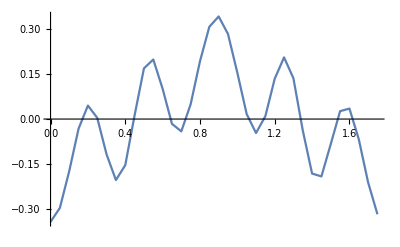

```mathematica
l=3;
m=1;
k=3;

ω = m Ωϕ + k Ωθ;


ListLinePlot[Table[{λ,SpinWeightedSpheroidalHarmonicS[0,l,m,a ω,θ[λ],0]Cos[ω t[λ]-m ϕ[λ]]},{λ,0,(2π)/Υ,.05}]]
```

```mathematica
Table[{λ,SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ + 2 Ωθ),θ[λ],0]},{λ,0,(2π)/Υ,.05}]-Table[{λ,SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ + 3 Ωθ),θ[λ],0]},{λ,0,(2π)/Υ,.05}]
```

{{0.,-0.000046627},{0.,-0.0000492797},{0.,-0.0000560864},{0.,-0.0000637481},{0.,-0.0000677215},{0.,-0.0000642742},{0.,-0.0000528812},{0.,-0.0000372832},{0.,-0.0000240853},{0.,-0.0000193972},{0.,-0.000025462},{0.,-0.0000393843},{0.,-0.0000547691},{0.,-0.0000652267},{0.,-0.000067562},{0.,-0.0000628359},{0.,-0.0000550364},{0.,-0.0000486364},{0.,-0.000046676},{0.,-0.0000500005},{0.,-0.0000571538},{0.,-0.0000645934},{0.,-0.0000677437},{0.,-0.0000631732},{0.,-0.0000509137},{0.,-0.0000352257},{0.,-0.0000228666},{0.,-0.0000195972},{0.,-0.0000269845},{0.,-0.0000415114},{0.,-0.0000565638},{0.,-0.0000660275},{0.,-0.0000672719},{0.,-0.0000618683},{0.,-0.0000540138},{0.,-0.0000480756}}

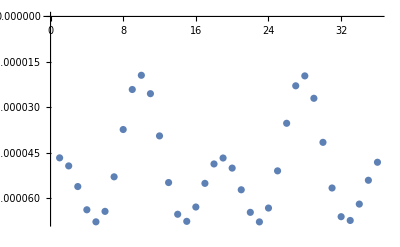

```mathematica
Flatten[List[{Table[{SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ + 2 Ωθ),θ[λ],0]},{λ,0,(2π)/Υ,.05}]-Table[{SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ + 3 Ωθ),θ[λ],0]},{λ,0,(2π)/Υ,.05}]}]]//ListPlot
```

```mathematica
ListLinePlot[Table[{λ,SpinWeightedSpheroidalHarmonicS[0,l,m,a ω,θ[λ],0]},{λ,0,(2π)/Υ,.05}]]
```

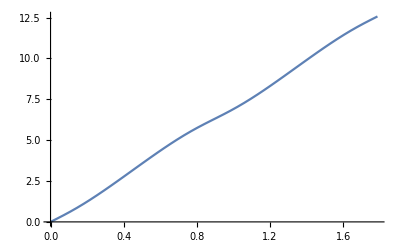

```mathematica
Plot[ω t[λ]-m ϕ[λ],{λ,0,(2π)/Υ}]
```